```mathematica
ClearAll["Global`*"]
NotebookDirectory[] ;
SetDirectory[%];
```

```mathematica
udata=ReadList["Geff.dat", {Number,Number}];
cdatah=ReadList["cdatah.txt",{Number,Number}];
```

```mathematica
rudata=Join[udata,cdatah];
```

```mathematica
u=Interpolation[rudata];
ru[r_]:=Piecewise[{{1,0≤r<0.01},{u[r],0.01<=r≤201.5},{1,r>201.5}}];
```

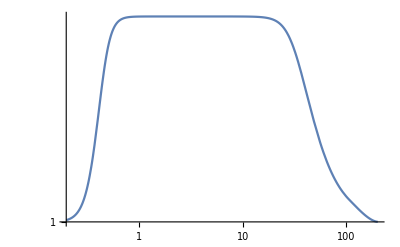

```mathematica
LogLogPlot[ru[r],{r,0,201.5}]
```

```mathematica
(*du=D[u[r],r];
rdu[r_]:=Piecewise[{{0,0≤r<0.01},{du,0.01<=r≤201.5},{0,r>201.5}}]*)
```

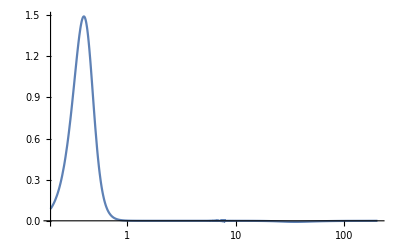

```mathematica
(*LogLinearPlot[rdu[r],{r,0,201.5},PlotRange->All]*)
```

```mathematica
(*rdudata=Table[{x,rdu[x]},{x,0,1,0.01}];
rduf=Interpolation[rdudata];
rrduf[r_]:=Piecewise[{{rduf[r],0<=r≤1},{0,r>1}}]*)
```

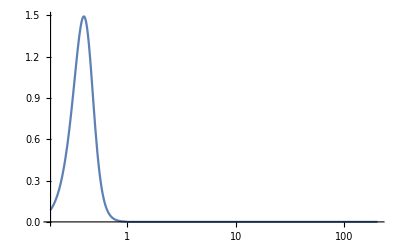

```mathematica
(*LogLinearPlot[rrduf[r],{r,0,201.5},PlotRange->All]*)
```

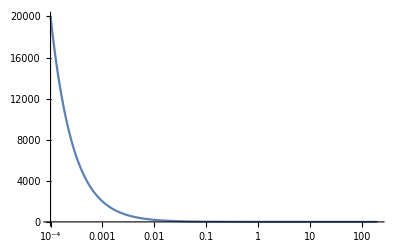

```mathematica
(*a1[b_]:=b*NIntegrate[((1+ru[r])*ru[r])/r^3/.r->√(b^2+z^2),{z,0,∞}]
LogLinearPlot[a1[b],{b,0.0001,201.5},PlotRange->All]*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.363604}. NIntegrate obtained 5.0308 and 0.000485539 for the integral and error estimates.

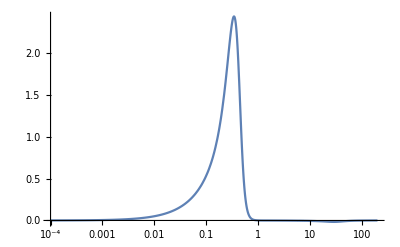

```mathematica
(*a2[b_]:=b*NIntegrate[((1+ru[r])*rdu[r])/r^2/.r->√(b^2+z^2),{z,0,Infinity}]
LogLinearPlot[a2[b],{b,0.0001,201.5},PlotRange->All]
*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.363604}. NIntegrate obtained 2.65731 and 0.000254568 for the integral and error estimates.

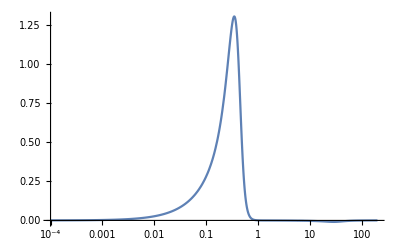

```mathematica
(*a3[b_]:=b*NIntegrate[(ru[r]*rdu[r])/r^2/.r->√(b^2+z^2),{z,0,Infinity}]
LogLinearPlot[a3[b],{b,0.0001,201.5},PlotRange->All]*)
```

```mathematica
(*Ibdata1=Table[{b,a1[b]-a2[b]-a3[b]},{b,0.001,1,0.001}];
Ibdata2=Table[{b,a1[b]-a2[b]-a3[b]},{b,1.01,201.5,0.01}];
*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.363554}. NIntegrate obtained 5.03082 and 0.000484801 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.363554}. NIntegrate obtained 2.65732 and 0.000254166 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.363403}. NIntegrate obtained 5.03095 and 0.000532808 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {7.59253}. NIntegrate obtained 0.000675049 and 0.0000277841 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {7.59253}. NIntegrate obtained 0.000393811 and 0.0000158617 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {7.86002}. NIntegrate obtained 0.000520056 and 0.0000252571 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
(*Ibdata3=Table[{b,a1[b]-a2[b]-a3[b]},{b,0.00101,0.00199,0.00001}];*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.363553}. NIntegrate obtained 5.03082 and 0.000484785 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.363553}. NIntegrate obtained 2.65732 and 0.000254158 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.363552}. NIntegrate obtained 5.03082 and 0.00048477 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.00101,1980.19},{0.00102,1960.78},{0.00103,1941.74},{0.00104,1923.07},{0.00105,1904.76},{0.00106,1886.79},{0.00107,1869.15},{0.00108,1851.85},{0.00109,1834.86},{0.0011,1818.18},{0.00111,1801.8},{0.00112,1785.71},{0.00113,1769.91},{0.00114,1754.38},{0.00115,1739.13},{0.00116,1724.13},{0.00117,1709.4},{0.00118,1694.91},{0.00119,1680.67},{0.0012,1666.66},{0.00121,1652.89},{0.00122,1639.34},{0.00123,1626.01},{0.00124,1612.9},{0.00125,1600.},{0.00126,1587.3},{0.00127,1574.8},{0.00128,1562.5},{0.00129,1550.38},{0.0013,1538.46},{0.00131,1526.71},{0.00132,1515.15},{0.00133,1503.75},{0.00134,1492.53},{0.00135,1481.48},{0.00136,1470.58},{0.00137,1459.85},{0.00138,1449.27},{0.00139,1438.84},{0.0014,1428.57},{0.00141,1418.43},{0.00142,1408.45},{0.00143,1398.6},{0.00144,1388.88},{0.00145,1379.3},{0.00146,1369.86},{0.00147,1360.54},{0.00148,1351.35},{0.00149,1342.28},{0.0015,1333.33},{0.00151,1324.5},{0.00152,1315.78},{0.00153,1307.18},{0.00154,1298.7},{0.00155,1290.32},{0.00156,1282.05},{0.00157,1273.88},{0.00158,1265.82},{0.00159,1257.86},{0.0016,1249.99},{0.00161,1242.23},{0.00162,1234.56},{0.00163,1226.99},{0.00164,1219.51},{0.00165,1212.11},{0.00166,1204.81},{0.00167,1197.6},{0.00168,1190.47},{0.00169,1183.43},{0.0017,1176.46},{0.00171,1169.58},{0.00172,1162.78},{0.00173,1156.06},{0.00174,1149.42},{0.00175,1142.85},{0.00176,1136.36},{0.00177,1129.94},{0.00178,1123.59},{0.00179,1117.31},{0.0018,1111.1},{0.00181,1104.97},{0.00182,1098.89},{0.00183,1092.89},{0.00184,1086.95},{0.00185,1081.07},{0.00186,1075.26},{0.00187,1069.51},{0.00188,1063.82},{0.00189,1058.19},{0.0019,1052.62},{0.00191,1047.11},{0.00192,1041.66},{0.00193,1036.26},{0.00194,1030.92},{0.00195,1025.63},{0.00196,1020.4},{0.00197,1015.22},{0.00198,1010.09},{0.00199,1005.02}}

```mathematica
(*Ibdatan=Join[Ibdata1,Ibdata2,Ibdata3];*)
```

```mathematica
(*Ibdata=Sort[Ibdatan,#1[[1]]<#2[[1]]&];*)
```

```mathematica
(*Export["Ibdata.txt",Ibdata,"Table"];*)
```

```mathematica
Ibdata=ReadList["Ibdata.txt",{Number,Number}];
```

```mathematica
rIb=Interpolation[Ibdata];
```

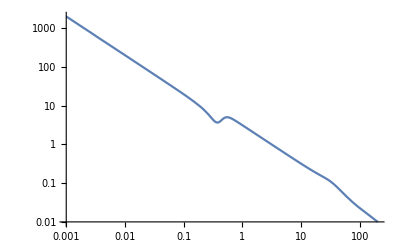

```mathematica
rrIb[b_]:=Piecewise[{{2/b,b<-201.5},{-rIb[-b],-201.5≤b≤-0.001},{2/b,-0.001<b<0.001},{rIb[b],0.001<=b≤201.5},{2/b,b>201.5}}];
LogLogPlot[rrIb[b],{b,0.001,201.5},PlotRange->All]
```

```mathematica
(*LogLogPlot[{a1[b]-a2[b]-a3[b],rrIb[b]},{b,0.01,110},PlotRange->All]*)
```

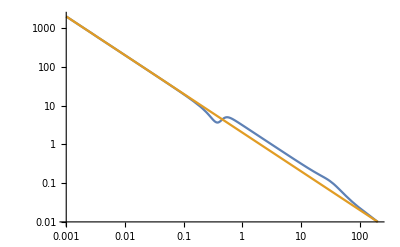

```mathematica
LogLogPlot[{rrIb[b],2/b},{b,0.001,201.5},PlotRange->All]
```

```mathematica
(*Itbdata=Table[{Ibdata[[i,1]],Ibdata[[i,2]]/Ibdata[[i,1]]},{i,1,Length[Ibdata]}];*)
```

```mathematica
(*Export["Itbdata.txt",Itbdata,"Table"];*)
```

```mathematica
Itbdata=ReadList["Itbdata.txt",{Number,Number}];
```

```mathematica
rItb=Interpolation[Itbdata];
```

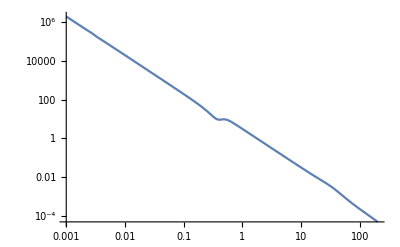

```mathematica
rrItb[b_]:=Piecewise[{{2/b^2,b<-201.5},{rItb[-b],-201.5≤b≤-0.001},{2/b^2,-0.001<b<0.001},{rItb[b],0.001<=b≤201.5},{2/b^2,b>201.5}}];
LogLogPlot[rrItb[b],{b,0.001,201.5},PlotRange->All]
```

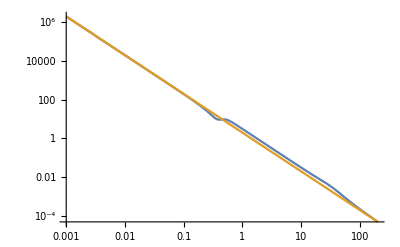

```mathematica
LogLogPlot[{rrItb[b],2/b^2},{b,0.001,201.5},PlotRange->All]
```

```mathematica
zl=0.3;
zs=1;
om=0.3;
h0=70;(*km s^-1 Mpc^-1*)
h0c=68;(*km s^-1 Mpc^-1*)
c=3*10^5;(*km s^-1*)
(*Mpc=30.85678*10^18 km*)
(*Msun=1.9891*10^30 kg*)
(*G=6.673*10^-11 m^3 kg^-1 s^-2*)
G=6.673*10^-20*1.9891*10^30;(*km^3 Msun^-1 s^-2*)
M=10^15;(*Msun*)
sigmav=300;(*km s^-1*)
```

```mathematica
H[t_]:=Sqrt[1-om+om *(1+t)^3];
DA[z_]:=c/h0 1/(1+z)NIntegrate[1/H[t],{t,0,z}];
DAc[z_]:=c/h0c 1/(1+z)NIntegrate[1/H[t],{t,0,z}];
DA2[z1_,z2_]:=c/h0 1/(1+z2)NIntegrate[1/H[t],{t,z1,z2}];
DA2c[z1_,z2_]:=c/h0c 1/(1+z2)NIntegrate[1/H[t],{t,z1,z2}];

DA[zl]
DA[zs]
DA2[zl,zs]
DA2[zl,zs]/(DA[zl]*DA[zs])

DAc[zl]
DAc[zs]
DA2c[zl,zs]
DA2c[zl,zs]/(DAc[zl]*DAc[zs])
```

919.403

1653.06

1055.45

0.000694452

946.444

1701.68

1086.49

0.00067461

```mathematica
thetaE=(4Pi*sigmav^2)/c^2*DA2[zl,zs]/DA[zs]
thetaEc=(4Pi*sigmav^2)/c^2*DA2c[zl,zs]/DAc[zs]
thetaE*DA[zl]
```

8.02339×10^-6

8.02339×10^-6

0.00737673

```mathematica
rhoSISGR[r_]:=sigmav^2/(2*Pi*G)*30.85678*10^18*1/r^2;
```

```mathematica
SigmaSISGR[ksi_]:=sigmav^2/(2*G)*30.85678*10^18*1/ksi;
```

```mathematica
alphaSISGR[ksi_]:=(4Pi*sigmav^2)/c^2*DA2[zl,zs]/DA[zs];
```

```mathematica
rhoSISMG[r_]:=sigmav^2/(2*Pi*G)*30.85678*10^18*1/(ru[r]*r^2);
```

```mathematica
SigmaSISMG[ksi_]:=2NIntegrate[rhoSISMG[r]/.r->(ksi^2+z^2)^(1/2),{z,0,Infinity}];
```

```mathematica
alphaSISMG[ksi_]:=(2*G)/c^2*1/(30.85678*10^18)*NIntegrate[ksip*SigmaSISMG[ksip]*(ksi-ksip*Cos[phi])*rrItb[(ksi^2+ksip^2-2ksi*ksip*Cos[phi])^(1/2)],{phi,0,2Pi},{ksip,0,Infinity}];
```

```mathematica
LogLogPlot[{alphaSISGR[ksi],alphaSISMG[ksi]},{ksi,0.001,201.5},PlotRange->All]
```

NIntegrate::inumr: The integrand (3.32993×10^12)/((ksip^2+z^2) (Piecewise[{{1, 0≤√Plus[«2»]<0.01}, {InterpolatingFunction[{{«2»}},{5,7,0,{«1»},{«1»},0,0,0,0,Automatic,{},{},False},{{«20150»}},{Developer`PackedArrayForm,{«20151»},{«20150»}},{Automatic}][√Plus[«2»]], 0.01≤√Plus[«2»]≤201.5}, {1, √Plus[«2»]>201.5}, {0, True}}])) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in ksip near {phi,ksip} = {5.30379,8.20831×10^60}. NIntegrate obtained 1.31416×10^14 and 1.3895×10^11 for the integral and error estimates.

$Aborted

```mathematica
n=2000;
```

```mathematica
thetaGRpd=Table[0,{n}];
thetaGRmd=Table[0,{n}];
thetaGRcpd=Table[0,{n}];
thetaGRcmd=Table[0,{n}];
thetaMGpd=Table[0,{n}];
thetaMGmd=Table[0,{n}];
```

```mathematica
For[i=1,i≤n,i++,If[i≤500,y=0.001*(i-1),y=0.5+0.003*(i-501)];thetaGR=theta/.NSolve[theta-y*thetaE==(4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zs]DA[zl])*1/theta,theta];thetaGRc=theta/.NSolve[theta-y*thetaEc==(4G*M)/c^2*1/(30.85678*10^18)*DA2c[zl,zs]/(DAc[zs]DAc[zl])*1/theta,theta];
thetaGRp=thetaGR[[1]];
thetaGRm=thetaGR[[2]];
thetaGRpd[[i]]={y,thetaGRp};
thetaGRmd[[i]]={y,thetaGRm};
thetaGRcp=thetaGRc[[1]];
thetaGRcm=thetaGRc[[2]];
thetaGRcpd[[i]]={y,thetaGRcp};
thetaGRcmd[[i]]={y,thetaGRcm};
thetaMGp=theta/.FindRoot[theta-y*thetaE==DA2[zl,zs]/DA[zs]*(2G*M)/c^2*1/(30.85678*10^18)*rrIb[b]/.b->(DA[zl]*theta),{theta,thetaGRp}];
thetaMGm=theta/.FindRoot[theta-y*thetaE==DA2[zl,zs]/DA[zs]*(2G*M)/c^2*1/(30.85678*10^18)*rrIb[b]/.b->(DA[zl]*theta),{theta,thetaGRm}];
thetaMGpd[[i]]={y,thetaMGp};
thetaMGmd[[i]]={y,thetaMGm};]
```

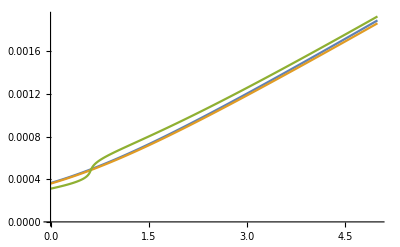

```mathematica
ListPlot[{thetaGRpd,thetaGRcpd,thetaMGpd},Joined->True,PlotRange->All]
```

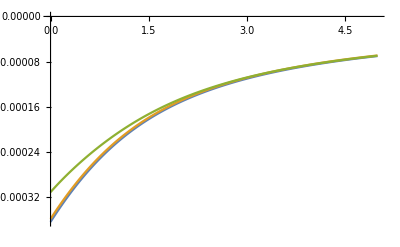

```mathematica
ListPlot[{thetaGRmd,thetaGRcmd,thetaMGmd},Joined->True,PlotRange->All]
```

```mathematica
min1=Min[Table[thetaGRpd[[i,2]],{i,1,n}],Table[thetaGRcpd[[i,2]],{i,1,n}],Table[thetaMGpd[[i,2]],{i,1,n}]]
```

0.000311635

```mathematica
max1=Max[Table[thetaGRpd[[i,2]],{i,1,n}],Table[thetaGRcpd[[i,2]],{i,1,n}],Table[thetaMGpd[[i,2]],{i,1,n}]]
```

0.00192792

```mathematica
min2=Min[Table[thetaGRmd[[i,2]],{i,1,n}],Table[thetaGRcmd[[i,2]],{i,1,n}],Table[thetaMGmd[[i,2]],{i,1,n}]]
```

-0.000364371

```mathematica
max2=Max[Table[thetaGRmd[[i,2]],{i,1,n}],Table[thetaGRcmd[[i,2]],{i,1,n}],Table[thetaMGmd[[i,2]],{i,1,n}]]
```

-0.0000692002

```mathematica
Min[Abs[min1],Abs[min2],Abs[max1],Abs[max2]]
```

0.0000692002

```mathematica
Max[Abs[min1],Abs[min2],Abs[max1],Abs[max2]]
```

0.00192792

```mathematica
phihGR[x_]:=(4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zl]*DA[zs])Log[Abs[x]];
phihGRc[x_]:=(4G*M)/c^2*1/(30.85678*10^18)*DA2c[zl,zs]/(DAc[zl]*DAc[zs])Log[Abs[x]];
phihMGini[x_]=yy[x]/.NDSolve[{yy'[theta]==DA2[zl,zs]/DA[zs]*(2*G*M)/c^2*1/(30.85678*10^18)*rrIb[b]/.b->(DA[zl]*theta),yy[0.002]==0},yy,{theta,0.000069,0.002},Method->"ExplicitRungeKutta"][[1]];
phihMG[x_]=phihMGini[Abs[x]];
```

```mathematica
TDGR=Table[0,{n}];
TDGRc=Table[0,{n}];
TDMG=Table[0,{n}];
```

```mathematica
For[i=1,i≤n,i++,thetaGRp=thetaGRpd[[i,2]];y=thetaGRpd[[i,1]];thetaGRm=thetaGRmd[[i,2]];
alphaGRp=thetaGRp-y*thetaE;
alphaGRm=thetaGRm-y*thetaE;
DettGR=(1+zl)/c*30.85678*10^18*(DA[zl]*DA[zs])/DA2[zl,zs](1/2(alphaGRm)^2-1/2(alphaGRp)^2-(phihGR[thetaGRm]-phihGR[thetaGRp]));
TDGR[[i]]={y,DettGR};

thetaGRcp=thetaGRcpd[[i,2]];y=thetaGRcpd[[i,1]];thetaGRcm=thetaGRcmd[[i,2]];
alphaGRcp=thetaGRcp-y*thetaEc;
alphaGRcm=thetaGRcm-y*thetaEc;
DettGRc=(1+zl)/c*30.85678*10^18*(DAc[zl]*DAc[zs])/DA2c[zl,zs](1/2(alphaGRcm)^2-1/2(alphaGRcp)^2-(phihGRc[thetaGRcm]-phihGRc[thetaGRcp]));
TDGRc[[i]]={y,DettGRc};
thetaMGp=thetaMGpd[[i,2]];y=thetaMGpd[[i,1]];thetaMGm=thetaMGmd[[i,2]];
alphaMGp=thetaMGp-y*thetaE;
alphaMGm=thetaMGm-y*thetaE;
DettMG=(1+zl)/c*30.85678*10^18*(DA[zl]*DA[zs])/DA2[zl,zs](1/2 alphaMGm^2-1/2 alphaMGp^2-(phihMG[thetaMGm]-phihMG[thetaMGp]));
TDMG[[i]]={y,DettMG};]
```

```mathematica
(*TDMG=ReadList["TDMG.txt",{Number,Number}];*)
```

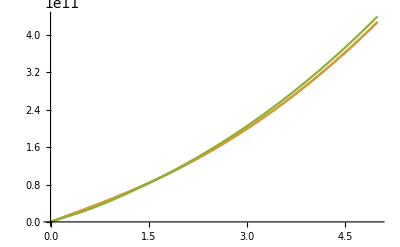

```mathematica
ListPlot[{TDGR,TDGRc,TDMG},Joined->True,PlotRange->All]
```

```mathematica
diffhc=Table[{TDGR[[i,1]],(TDGRc[[i,2]]-TDGR[[i,2]])/TDGR[[i,2]]},{i,2,Length[TDMG]}];
diffMG=Table[{TDGR[[i,1]],(TDMG[[i,2]]-TDGR[[i,2]])/TDGR[[i,2]]},{i,2,Length[TDMG]}];
(*diffMGc=Table[{TDGRt[[i,1]],(TDMGt[[i,2]]-TDGRct[[i,2]])},{i,1,Length[TDMGt]}];*)
```

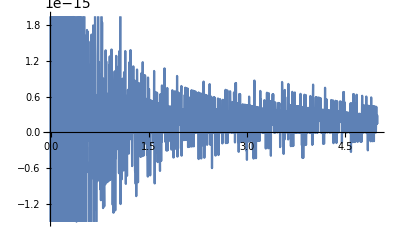

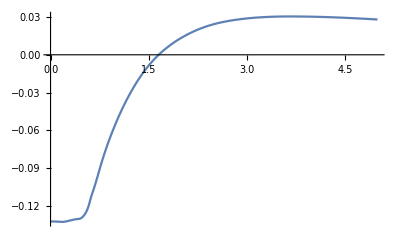

```mathematica
ListLinePlot[diffhc]
ListLinePlot[diffMG]
(*ListLinePlot[diffMGc]*)
```

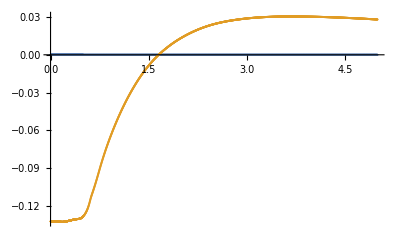

```mathematica
ListPlot[{diffhc,diffMG},PlotRange->All]
```

```mathematica
Export["thetaGRpd.txt",thetaGRpd,"Table"];
Export["thetaGRcpd.txt",thetaGRcpd,"Table"];
Export["thetaMGpd.txt",thetaMGpd,"Table"];
Export["thetaGRmd.txt",thetaGRmd,"Table"];
Export["thetaGRcmd.txt",thetaGRcmd,"Table"];
Export["thetaMGmd.txt",thetaMGmd,"Table"];
```

```mathematica
Export["TDGR.txt",TDGR,"Table"];
Export["TDGRc.txt",TDGRc,"Table"];
Export["TDMG.txt",TDMG,"Table"];
```